```mathematica
Ns=128;
Nc=2;
Nxy=16;
NN=Nxy*Nxy;
M=1000;
```

```mathematica
SS=Array[0&,{M,Nxy,Nxy}];
CC=Array[0&,{NN,NN}];
SeedRandom[1];

For[ic=0,ic<=M-1,ic++,
For[iy=0,iy<=Nxy-1,iy++,
For[ix=0,ix<=Nxy-1,ix++,
SS[[ic+1,ix+1,iy+1]]=Cos[ix*Pi/2]+Cos[iy*Pi/2]+0.1Random[Real,{-1,1}]
]
]
]
```

```mathematica
start=SessionTime[];
For[j=0,j<=NN-1,j++,
jx=Mod[j,Nxy];
jy=Floor[j/Nxy];
For[i=0,i≤NN-1 ,i++,
ix=Mod[i,Nxy];
iy=Floor[i/Nxy];
sumij=0.;
sumi=0.;
sumj=0.;
For[ic=0,ic<=M-1,ic++,
sumij+=SS[[ic+1,ix+1,iy+1]]*SS[[ic+1,jx+1,jy+1]];
sumi+=SS[[ic+1,ix+1,iy+1]];
sumj+=SS[[ic+1,jx+1,jy+1]];
];
CC[[i+1,j+1]]=sumij/M-sumi/M*sumj/M;
]
]
SessionTime[]-start
```

388.967242

```mathematica
CCmax=Max[CC]
CCmin=Min[CC]
CCm=Max[Abs[CCmax],Abs[CCmin]]
ListDensityPlot[CC,InterpolationOrder->0,PlotRange->{-CCm/2,CCm/2},PlotLegends->Automatic,ColorFunction->"RedBlueTones"]
```

0.00356382

-0.000412658

0.00356382

-Graphics-

```mathematica
{Evals,Evecs}=Eigensystem[CC];
```

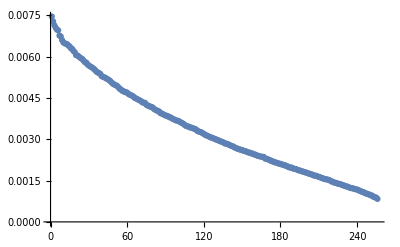

```mathematica
ListPlot[Evals]
```

```mathematica
(*Counts of {positive, negative} Eigenvalues*)
{Count[Evals,u_/;u>0],Count[Evals,u_/;u<0]}
```

{256,0}

```mathematica
(*
window,1,xsize=Ns*M+Nc*(M-1),ysize=Ns,xpos=600,ypos=0
for ic=0,M-1 do begin
tvscl,congrid(S[*,*,ic],Ns,Ns),ic*(Ns+Nc),0
endfor
filename=FILEPATH('S.png',ROOT_DIR='C:\Users\Jhinhwan Lee\Desktop\')
WRITE_PNG,filename,TVRD(/TRUE)
PRINT,'File written to',filename

window,2,xsize=4*N*2,ysize=4*N,xpos=600,ypos=600
tvscl,congrid(C,4*N,4*N)
tvscl,congrid(C LT 0,4*N,4*N),4*N,0
filename=FILEPATH('C.png',ROOT_DIR='C:\Users\Jhinhwan Lee\Desktop\')
WRITE_PNG,filename,TVRD(/TRUE)
PRINT,'File written to',filename

EVC=C
TRIRED,EVC,EVL,EE;, /DOUBLE
TRIQL,EVL,EE,EVC;, /DOUBLE

PRINT,'Eigenvalues:'
PRINT,EVL
E=dblarr(Nxy,Nxy,N)

MM=32
window,3,xsize=Ns*MM+Nc*(MM-1),ysize=(Ns+30)*8,xpos=0,ypos=200
FOR l=0,7 DO BEGIN
FOR i=0,MM-1 DO BEGIN
id=i+l*MM
E[*,*,id]=EVC[*,id]
tvscl,congrid(E[*,*,id],Ns,Ns),i*(Ns+Nc),l*(Ns+30)
xyouts,i*(Ns+Nc),l*(Ns+30)+Ns+4,string(EVL[id]),/DEVICE,CHARSIZE=0.7,CHARTHICK=(abs(EVL[id]) GT 1)?2.:1.
ENDFOR
ENDFOR

filename=FILEPATH('I.png',ROOT_DIR='C:\Users\Jhinhwan Lee\Desktop\')
WRITE_PNG,filename,TVRD(/TRUE)
PRINT,'File written to',filename

end
*)
```